# Empirical P vs. NP: When Different Turing Machines Compute the Same Function

Michael Sun

Wolfram High School Summer Research Program 2025

A Turing machine is a theoretical model of computation classified as an automaton invented by Alan Turing that operates on an infinite tape of sequential memory. The significance of Turing machines, as described in the Church-Turing thesis, comes from their ability to compute any function and therefore have the same computational ability as all conventional computers. Empirical evidence suggests that there exists Turing machines that follow different rules but ultimately compute the same function, presumably for all inputs. Naturally, these machines will have different runtimes, which models multiple computers running different algorithms to reach the same goal. Similarly, motivation for studying complexity theory comes from analyzing and improving algorithms. A central unsolved problem in the field is if quickly verifying a solution to a problem implies the existence of an algorithm that quickly solves it—commonly known as the P vs. NP problem. Analyzing patterns in the range of runtimes for equivalent Turing machines provides potential for empirically guessing at whether P equals NP.

## Introduction

Formally, Turing machines are tuples containing a set of states, a halt state, a set of symbols called its alphabet, and a lookup table of all possible state-symbol pairs. Turing machines keep a pointer to the cell it is currently reading, and the symbol on this cell combined with its current state defines a transition. For each transition, three operations occur: read the symbol on the current cell, write a (not necessarily distinct) symbol to the current cell, and move to an adjacent cell. Certain traits of a Turing machine are difficult to quickly represent with a computer, so the results in this essay will be close approximations of the real behavior of Turing machines. Specifically, we will bound a finite section of the tape and set a halting condition not dependent on its state for convenience. Additionally, we will focus on 2-symbol Turing machines since any machine can be reduced to a 2-symbol Turing machine.

### Terminology

In this essay, the variables  and  generally refer to the  states and  symbols of a Turing machine, and the ordered pair  refers to an -state -symbol Turing machine. Additionally, I define setting a Turing machine to a nonnegative integer  as filling our chosen interval  of the tape of length  for some  with the binary representation of  in big endian (natural left-to-right order). We ensure that  (i.e. the number of bits fits in ). Additionally, I define the value of a Turing machine as the number created by each cell on  as base- digits where the blank symbol translates to zero (which is automatic in the Wolfram Language).

### Formalism

Let  be the set of all -state -symbol Turing machines. Each machine in  represents a partial function  with input specified by the base  number formed by the closed interval  on the tape, where each symbol is an integer between 0 and . Define two Turing machines in  to be equivalent if they compute the same partial function on , or both do not exist. The number of distinct machines is the cardinality of . For each equivalence class, we will analyze patterns of the worst-case running times of each machine in the class and over all classes in  for different  and .

For example, the following 2-state 2-symbol Turing machine takes in  where 1’s are colored orange. The output is read as . It turns out that this rule always adds 1 to the input for our constraints.

Evolution of the partial (and total) function  described by rule 451 for  and input :

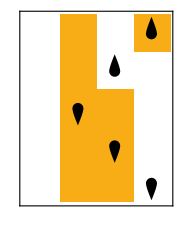

```mathematica
RulePlot[TuringMachine[445],{{1,4},{IntegerDigits[5,2,4],0}},4,ImageSize->Small]
```

## Theory

Only certain  pairs are capable of simulating any other Turing machine starting from a blank tape. For example, any Turing machine with one symbol trivially fails to be universal because it will not edit the tape. Pairs that can simulate all other machines are known as universal Turing machines. Additionally, weakly universal Turing machines are machines that are universal on an arbitrary initial tape. Notably, the smallest of these machines are fully analyzable within computational constraints, such as (3, 3), (2, 4), and Wolfram’s (2,3) machine, which we will focus on in this essay.

The universality of Turing machines as a mathematical model of computation revealed the limits of computing, notably cases of logical (un)decidability. A problem is undecidable if and only if it is provable that there exists no algorithm that will always return the correct answer to the problem. Turing’s major result was his proof of the undecidability of determining if a computer program halts, famously known as the halting problem.

### The Halting Problem and Rice’s Theorem

The usefulness of the undecidability of the halting problem is not only limited to the statement itself, but because many problems can be shown to be undecidable by reducing them to the halting problem. More notably, it is undecidable to determine if two Turing machines are equivalent, which necessitates the mentioned constraints. Similarly, the task to quickly analyze the behavior of a Turing machine without simulating it is a generalization of the halting problem known as Rice’s theorem, which implies that this task is generally undecidable. However, it does not say anything about determining relationships between machines, which we will see in a later section could contain a predictable pattern.

## Implementation

Due to the undecidability of universal static analysis and the computational irreducibility of Turing machine evolution, the implementation will inevitably be brute-force in nature. However, there are certain ways to prune the search space by examining only the rules. There are also optimizations for Turing machine simulation, particularly with memoizing sections of the tape.

### Pruning

Despite the undecidability of finding a universal way of reducing computation across Turing machines or even on one Turing machine, we can take inspiration from DFA (deterministic finite automaton) minimization. Specifically, one big optimization we can make is to declare that all Turing machines with rules that permute a dead state (unreachable from the initial state) to be equal: each of these permutations are unreachable anyway.

The diagram below shows two equivalent Turing machines, each with a different permutation of the rules from state 2, which is unreachable from state 1.

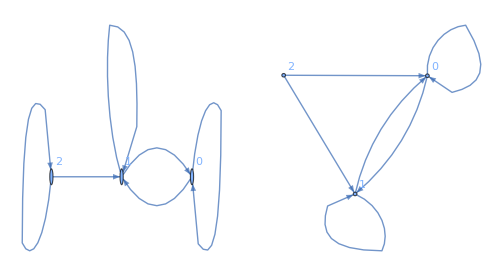

```mathematica
GraphicsRow[{
Graph[{1->1,1->0,0->1,0->0,2->1,2->2},VertexLabels->Automatic],
Graph[{1->1,1->0,0->1,0->0,2->0,2->1},VertexLabels->Automatic]
}]
```

Determining the reachable nodes reduces to graph traversal. It is not hard to see that all state graphs have  vertices and  edges, resulting in a runtime of .

The numbering system of Turing machines in the Wolfram Language permutes rules in the following order: direction (-1 to 1), symbol (0 to ), then state (1 to ). For the rest of the essay, we will use this numbering without loss of generality. Notice that for consecutive unreachable states ending in state  (e.g. 2, 3 for ), their rule numbers will also be grouped separately so we only need to define the interval (start and end) of rule numbers of an equivalence class. For example, suppose that state 3 is unreachable for . Then there exists contiguous intervals of rules that are isomorphic, such as rules 83520 to 84096. Thus, for each of these blocks, we can skip ahead to the end of a block when we encounter its beginning. Consequently, this is also the only time we can speed up iteration.

The length of an iteration depends on the number of reachable states. If there are  reachable states from 1 to , then there are  unreachable states. The number of ways we can permute these unreachable states is given by , since there are  symbols per state and  ways to permute each single component of a rule.

Set number of states and symbols:

```mathematica
states=3;
symbols=2;
machines=(2*states*symbols)^(states*symbols);
```

getinfo requires the full form of a rule, but rule numbers are easier to comprehend, so we will use the following two resource functions to convert between them.

Resource functions to convert between rule full form and rule number:

```mathematica
tmRuleFromNum=ResourceFunction["TuringMachineFromNumber"];
tmRuleToNum=ResourceFunction["TuringMachineToNumber"];
```

Gets the end states for each transition and generate a state diagram from the rule:

```mathematica
getinfo[r_]:={r[[All,2]],Graph[r[[All,All,1]]]}
```

The key construction will be to point all unreachable states to 1’s so that they map to the beginning of an equivalent block of rules if the condition is satisfied. Thus we can directly convert this rule to the rule number that represents the start of a potential block of rules with unreachable states, allowing us to easily skip ahead.

Transforms a return value from getinfo into a hash key such that all equivalent Turing machines have the same key:

```mathematica
cftransform=
FunctionCompile[
Function[
{
Typed[states,"MachineInteger"],
Typed[symbols,"MachineInteger"],
Typed[reachable,"PackedArray"::["MachineInteger",1]],
Typed[key,"PackedArray"::["MachineInteger",1]]
},
Flatten@
Table[
If[
MemberQ[reachable,j],
Flatten@Table[key[[k]],{k,3*symbols(j-1)+1,3*symbols*j}],
Table[1,3*symbols]
],
{j,states}
]
]
];
```

Returns :

```mathematica
perm[d_Integer]:=(2*states*symbols)^(symbols*(states-d))
```

Checks if l is a consecutive list that starts with 1:

```mathematica
consQ[l:{___Integer}]:=First[l]==1&&Most[l]+1===Rest[l]
consQ[_List]:=False
```

The following function is a block of “pseudo-procedural” code that determines the number of unique rules and the number of times each rule is repeated. To dynamically skip blocks of rules, we cannot take advantage of the optimized list manipulation functions and must use a For loop to truly avoid iterating through everything. To determine if the current rule is the start of a block, we do a graph traversal in  time. Thus we want to minimize the number of times this check is done. Do is more optimized than For but consequently has no easy way of jumping ahead, forcing us to always evaluate the array in  time. As the number of states and symbols increases, this approach becomes preferred since we are able to skip more values at once.

Takes in the number of rules to analyze from 0 to len-1 and loops through those rules, skipping if possible:

```mathematica
prune[len_Integer]:=
Module[{rcur,tmp,i},
For[
i=CreateDataStructure["Counter",0],
i["Get"]<len,
i["Increment"],
With[{info=getinfo[tmRuleFromNum[i["Get"],states,symbols]]},
rcur=VertexOutComponent[info[[2]],1];
map[
"Insert",
(#->map["Lookup",#,0&]
+If[
consQ[Sort[rcur]],
tmp=perm[Length[rcur]];i["AddTo",tmp-1];tmp,
1
]
)&@cftransform[states,symbols,rcur,Flatten@info[[1]]]
];
]
]
]
```

Call the function:

```mathematica
map=CreateDataStructure["HashTable"];
prune[machines];
elems=map["Elements"];
```

Or get precomputed data of (3, 2) from the cloud:

```mathematica
elems=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/18a0dc05-36a4-42da-b07c-fd940256d0f4"](https://www.wolframcloud.com/obj/18a0dc05-36a4-42da-b07c-fd940256d0f4)]];
```

We can confirm that equivalence classes (not just those that are consecutive) come in sizes of  for all nonnegative . In this case, for , we indeed have , , .

```mathematica
DeleteDuplicates[elems[[All,2]]]
```

{1,144,20736}

### Rule Extraction

Now we convert the rules back to their canonical numbered form for indexing during analysis and piece together information about each rule and its evolution. key stores the Turing machine rule keys, and vals stores the pruned rules, which are strung together to form a Turing machine rule. The list of keys should be of the form {{n,k-1},{n,k-2},...,{n,1},{n,0},{n-1,k-1},...,{1,0}}, which can be produced by transposing  length  arrays with a length  consecutive decreasing sequence modulo .

Reconstruct full form rules:

```mathematica
fullRules=With[
{
key=Transpose@{
Flatten@Table[ConstantArray[i,symbols],{i,states}],
Table[Mod[i,symbols],{i,states*symbols-1,0,-1}]
},
vals=Partition[#[[1]],3]&/@elems
},
ParallelMap[Table[key[[i]]->#[[i]],{i,states*symbols}]&,vals]
];
```

Convert full form rules to numbered rules:

```mathematica
ruleNumsCompressed=Map[tmRuleToNum[#][[1]]&,fullRules];
```

Or get precomputed data from the cloud:

```mathematica
ruleNumsCompressed=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/e5e6b260-f207-4614-8856-fe336facc2cf"](https://www.wolframcloud.com/obj/e5e6b260-f207-4614-8856-fe336facc2cf)]];
```

Free memory:

```mathematica
fullRules=.
```

### Search

As mentioned, the behavior of a Turing machine is undecidable even on a finite tape, so we must optimize our simulation method. One notable bottleneck—amongst others—is repeating and non-terminating Turing machines. Optimizing repeating machines can be naturally solved by memoizing a “snapshot” of the Turing machine for each independent round of simulation of a machine and an input. After each iteration, we check if the current snapshot has been seen before. If we arrive from a snapshot back to the same snapshot, we know we have a loop and we can terminate. Further, since we test all inputs from 0 to 2^(bits-1) for the same Turing machine, we can keep a persistent collection of snapshots between inputs for each Turing machine. A snapshot of a Turing machine consists of the tuple  where  is the cell the Turing machine is currently pointing to and  is the DP radius.

The TuringMachine function likely contains internal optimizations for evolving the Turing machine for multiple states at a time, so individual iterations of TuringMachine in a NestWhile will be much slower. However, we inherently need to iterate to avoid slowdowns with running many more iterations than we need to. To solve this, we can iterate through blocks of Turing machines to leverage optimization from both aspects.

The other arguably more significant bottleneck is when a Turing machine predictably moves in the same direction (particularly away from its start). I believe there is a way to extend our current DP implementation to account and optimize for this, but it is currently unimplemented.

Set the DP radius, tape width, and bits to enumerate

```mathematica
dprad=32;
width=64;
bits=5;
```

The following function gets the next block of transitions given the previous block used in a NestWhile. Since the TuringMachine function adds padding to its output, we trim each output to only include the specified interval we want to work with.

Gets the next block of evolutions of a Turing machine given the previous block:

```mathematica
stepTM[rule_Integer,stages_List,blockwidth_Integer]:=
With[
{tms=TuringMachine[{rule,states,symbols},stages[[-1]],blockwidth]},
Transpose@{
tms[[All,1]],
PadLeft[#[[2]],width,0,width-Length[#[[2]]]]&/@tms
}
]
```

Each invocation of the htDP function constructs DP tables as least frequently used (LFU) caches for speed and reduced memory overhead. Consequently, there is an upper bound to the number of snapshots that can be stored, but this limit should usually not be reached. In the following block of code, we have a NestWhile to compute each block of Turing machine evolutions, and within the body, we loop through each evolution with a While loop and update DP tables accordingly.

Generate the halting configuration for each rule:

```mathematica
htDP[rule_Integer,bits_Integer,blockwidth_Integer,maxdepth_Integer]:=
Transpose@
With[{dpG=CreateDataStructure["LeastRecentlyUsedCache",256]},
Table[
Module[
{
dp=CreateDataStructure["LeastRecentlyUsedCache",256],
i=CreateDataStructure["Counter",1],
cnt=CreateDataStructure["Counter",0],
tms,tmp,
flag=False,
cur={{0,0,0}}
},
tms=NestWhile[
stepTM[rule,#,blockwidth]&,
stepTM[rule,{{{1,width,0},{IntegerDigits[n,2,width],0}}},blockwidth],
(
i["Set",1];
While[
cur=#[[i["Get"]]];
i["Get"]<=blockwidth&&!flag&&cur[[1,3]]<=0,

tmp=Join[
{cur[[1,1]],cur[[1,3]]},
PadLeft[cur[[2]],2*dprad-1,0,dprad+cur[[1,3]]-1]
];
If[
!(flag=dpG["KeyExistsQ",tmp]),
If[
(flag=dp["KeyExistsQ",tmp]),
dpG["Insert",tmp->1],
dp["Insert",tmp->1]
]
];
i["Increment"];
cnt["Increment"];
];
i["Get"]==blockwidth+1&&!flag&&cur[[1,3]]<=0
)&,
1,maxdepth
];
Flatten[{
If[flag||cnt["Get"]==maxdepth*blockwidth,-1,cnt["Get"]],
If[tms[[i["Get"],1,3]]==1,FromDigits[tms[[i["Get"],2]],2],-1]
}]
],
{n,1,2^bits-1}
]
]
```

Call function in parallel. Wolfram internal parallelization functions should preserve order:

```mathematica
halts=ParallelMap[htDP[#,4,4,16]&,ruleNumsCompressed];
```

Join the computed information in the form of{rule, number times repeated, {halt times}, {halt values}}

```mathematica
haltconfig=Transpose@{
ruleNumsCompressed,
elems[[All,2]],
halts[[All,1]],
halts[[All,2]]
};
```

```mathematica
halts=.
```

Remove non-terminating machines and group each halting configuration in the form{{range, min, max, rules...}...}

```mathematica
haltgroups32=
Map[
With[
{ttl=Total[#[[All,2]]],mm=MinMax[Max[#[[3]]]&/@#]},
Flatten@{mm[[2]]-mm[[1]],mm,#[[All,1]]}
]&,
GatherBy[
Select[haltconfig,!ContainsOnly[#[[3]],{-1}]&],
#[[4]]&
]
];
```

## Distribution Analysis

In this section, we visualize our computed results and draw attention to key features of the graph and extrapolate on patterns. Note that all data fetched from the cloud were computed using the code in the previous section.

Generates a manipulable plot of runtime,

```mathematica
genplot[data_List]:=
With[
{
sup=Length@data,
sizsup=Max[Length/@data]-3,
step=IntegerPart[Length@data/400],
sizstep=IntegerPart[Max[Length/@data]/400]
},
Manipulate[
With[{
w=1000,
sorted=SortBy[
data,Switch[
sort,
"Runtime Range",-First[#]&,
"Class Size",-Length[#]&,
"Max Runtime",-#[[3]]&,
"Min Runtime",-#[[2]]&
]
]
},
Column[{
ListPlot[
((Length/@sorted)-3)[[Min[a,b];;b]],
Joined->True,
PlotRange->{{Automatic,Automatic},{Automatic,sizbound}},
ImageSize->{w,Automatic},
AspectRatio->1/16,
PlotLabel->"Equivalence Class Size"
],
ListPlot[
(First/@sorted)[[Min[a,b];;b]],
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/10,
PlotLabel->"Runtime Range"
],
ListPlot[
{sorted[[All,2]][[Min[a,b];;b]],sorted[[All,3]][[Min[a,b];;b]]},
Joined->True,
PlotRange->All,
ImageSize->{w,Automatic},
AspectRatio->1/6,
PlotLabel->"Maximum and Minimum Runtime",
PlotLegends->{"Min","Max"}
]
}]
],
{{a,1,"Left bound"},1,sup,step,Appearance->"Labeled"},
{{b,sup,"Right bound"},1,sup,step,Appearance->"Labeled"},
{{sort,"Runtime Range","Sort by"},{"Runtime Range","Class Size","Max Runtime","Min Runtime"}},
{{sizbound,sizsup,"Size upper bound"},50,sizsup,sizstep,Appearance->"Labeled"},
SaveDefinitions->True
]
]
```

Get and plot (3,2) data:

```mathematica
haltgroups32=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/cd09d92f-87f5-45cc-b958-f117a03cef75"](https://www.wolframcloud.com/obj/cd09d92f-87f5-45cc-b958-f117a03cef75)]];
genplot[haltgroups32]
```

Get and plot (2,3) data:

```mathematica
haltgroups23=CloudGet[CloudObject["https://www.wolframcloud.com/obj/fcc296dd-6d0b-4345-b5e7-1694ad35d0cd"]];
genplot[haltgroups23]
```

The plots of  and  Turing machines look almost identical, but running Complement on them shows that they differ slightly. Additionally, we see

```mathematica
Length@Complement[haltgroups32,haltgroups23]
```

412

Get and plot (2,2) data:

```mathematica
haltgroups22=CloudGet[CloudObject["https://www.wolframcloud.com/obj/7a908bdd-d24e-45a3-a1f2-04fc2ce8f7f5"]];
genplot[haltgroups22]
```

(4,2) plot for the first 68 million rules (the first 67108864 being split into four groups):

```mathematica
haltgroups42=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/70c01f90-a92b-4ca9-9cd4-e516dc85ba31"](https://www.wolframcloud.com/obj/70c01f90-a92b-4ca9-9cd4-e516dc85ba31)]];
genplot[haltgroups42]
```

(3,3) plot for the first 206 million Turing machines (the first 204073344 being split into six groups):

```mathematica
haltgroups33=CloudGet[CloudObject[["https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09"](https://www.wolframcloud.com/obj/1e1e1e10-681c-4346-b486-2ec3b138be09)]];
genplot[haltgroups33]
```

Notice that the shape of the minimum and maximum curves look almost identical in all  combinations presented here. Also, all plots have tall spikes on the right when sorting by runtime range where the runtime range is near zero. Sorting by class size, we see that each plot ends with an increasing curve, which represents the mentioned spikes in maximum runtime despite having very small class size. We also observe that given that the size of a set of equivalence classes is “sufficiently large”, the distribution of runtime ranges is seemingly unpredictable. See the (2,3) or (3,2) plots from 1 to 500 and (3,3) plot from 1 to 1000.

Rule Distribution

The following graphic depicts the distribution of rule numbers for the first 256 equivalence groups sorted from greatest runtime range to least. Each point  means that rule  is part of equivalence class , with many y-values for each x-value. Points near each other with the same color correspond to the same equivalence class.

```mathematica
stackPoints[l_List]:=MapIndexed[Function[{value,index},{First@index,#}&/@value]]@l
Rasterize[
ListPlot[
stackPoints[SortBy[haltgroups32,-First[#]&][[;;256,4;;]]],
PlotRange->Full,
ImageSize->{1200,Automatic},
AspectRatio->1/3,
PlotLabel->"Distribution of the First 256 Equivalence Classes, Sorted by Runtime Range",
PlotHighlighting->None,
AxesLabel->{"Equivalence class", "Rule number"},
PerformanceGoal->"Speed"
]
]
```

-Graphics-

We notice that many equivalence classes contain consecutive blocks of rules—a subset of these being state graphs that are not completely traversable from the initial state. However, most of the patterns are more nuanced than this, where there are small gaps between pseudo-consecutive rules belonging to the same equivalence class. Non-consecutive sets of rules that have unreachable states in their state graph form an arithmetic sequence and would have regularity on the graphic, but the intriguing part is that cases of unreachable states are relatively uncommon, yet for almost all equivalence classes shown, there is some form of regularity.

### Existing Work

By changing the state and symbol variables (e.g. in a Block), we can get results for different numbers of states and symbols. In this section, we show that for , our findings partially agree with Wolfram’s findings on page 761 of A New Kind of Science. He found that the set of all (2,2) Turing machines computes exactly 351 distinct functions (including the function that does not halt), which is the same number I found by evaluating for four bits with a maximum of 64 iterations. However, I found 368 unique machines when evaluating for eight bits with a maximum of 512 iterations.

4 bit numbers with 64 iterations:

```mathematica
CloudGet[CloudObject[["https://www.wolframcloud.com/obj/8b605cb9-0b20-4efd-a2f5-fa0545cb6b10"](https://www.wolframcloud.com/obj/8b605cb9-0b20-4efd-a2f5-fa0545cb6b10)]]//Length
```

350

8 bit numbers with 512 iterations:

```mathematica
haltgroups22//Length
```

368

### Runtime Analysis

Each equivalence class corresponding to a single -coordinate on the graphs above contain rules that differ in runtime despite computing the same function. This can be visualized similarly, and we can overlay graphs of common runtimes with manipulable parameters to manually match a runtime plot with a function.

Generate a plot for the runtime of each rule in an equivalence class:

```mathematica
genRuntimePlot[sorted_List,nstates_Integer,nsymbols_Integer,bits_Integer,l_Integer:1,r_Integer:-1]:=
Block[{states=nstates,symbols=nsymbols},
With[
{
data=DeleteDuplicates[
ParallelMap[
htDP[#,bits,8,64]&,
sorted[[3+l;;r]]
][[All,1]]
]
},
Manipulate[
Show[
Plot[dy,{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[loga*Log2[x+1]+dy,{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[lina*x+dy,{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[qa*x^2+dy,{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]}],
Plot[ea*2^x+dy,{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]}],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
PlotRange->{{1,2^bits},{0,Max[data]}},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
ImageSize->Large,
AxesLabel->{"Input number", "Runtime"}
],
{{dy,0,"y shift"},0,Max[data],Appearance->"Labeled"},
{{loga,1,"Logarithmic constant"},1,30,Appearance->"Labeled"},
{{lina,1,"Linear constant"},0.1,10,Appearance->"Labeled"},
{{qa,1,"Polynomial constant"},0.1,2,Appearance->"Labeled"},
{{ea,1,"Exponential constant"},0.1,2,Appearance->"Labeled"},
SaveDefinitions->True
]
]
]
```

Get sorted equivalence classes:

```mathematica
sorted22=SortBy[haltgroups22,-First@#&];
```

```mathematica
sorted23=SortBy[haltgroups23,-First@#&];
```

Generates an interactive plot for (2,2) group 13:

```mathematica
genRuntimePlot[sorted22[[13]],2,2,8]
```

Out of the first 20 equivalence classes for (2,2) machines, 10 groups generally had logarithmic behavior, and some groups seem to oscillate from 0 to a constant maximum. It is difficult to extrapolate the ultimate behavior of these oscillating plots, but I suspect they are most likely constant and possibly logarithmic. One of these graphs is group 2 (see below), which seems to model a triangle wave and thus be considered constant. However, group 10 may imply that the graphs like group 2 (potentially excluding itself) may be part of a larger graph that only becomes emergent for large inputs.

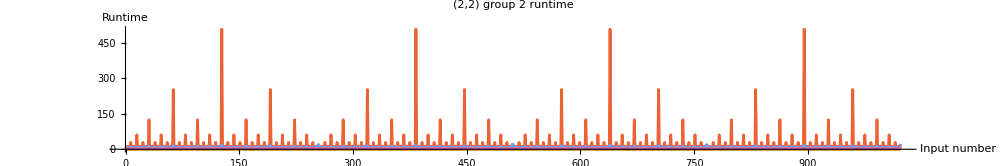

```mathematica
Block[{states=2,symbols=2,width=32},
With[
{
dx=2.5,
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,10,8,64]&,
sorted22[[2,4;;]]
][[All,1]]
]
},
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All,
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 2 runtime",
PerformanceGoal->"Speed"
]
]
]
```

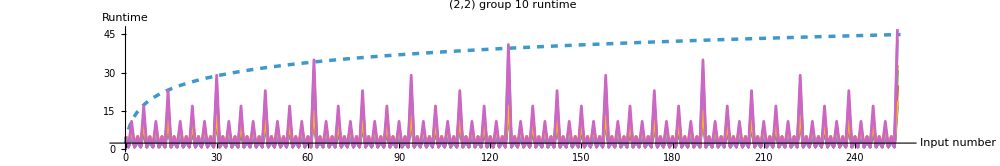

```mathematica
Block[{states=2,symbols=2},
With[
{
dx=2.5,
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted22[[10,4;;]]
][[All,1]]
]
},
Show[
Plot[5.3*Log2[x+1]+2.5,{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]},PlotRange->All],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
PlotRange->{{0,2^bits-1},{0,Max[data]}},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 10 runtime",
PerformanceGoal->"Speed"
]
]
]
```

For (2,3) machines, the overall behavior is harder to see generally because the number of rules in a group can be very large so we must process subsets of data at a time. We can also refer to the (2,3) graph at the beginning of the section and find groups that have small group size, such as 3, 8, 12, and 13. Generally, this subset of groups seems to show that (2,3) runtimes are more chaotic than (2,2). A notable group in (2,3) is group 12, where there is one Turing machine that seems to represent a total function that runs in constant time while all others run in approximately logarithmic time.

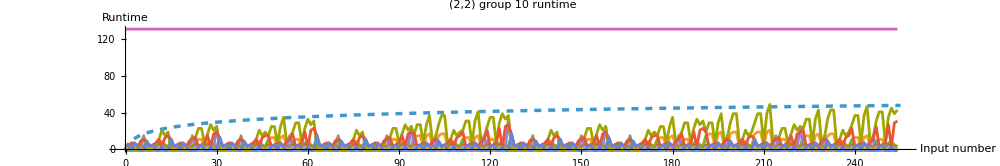

```mathematica
Block[{states=2,symbols=3},
With[
{
bits=8,
data=DeleteDuplicates[
ParallelMap[
htDP[#,8,8,64]&,
sorted23[[12,4;;]]
][[All,1]]
]
},
Show[
Plot[6*Log2[x+1],{x,0,2^bits-1},PlotStyle->{Dashed,Thickness[0.0025]},PlotRange->All],
ListPlot[
data,
DataRange->{0,Length@data[[1]]-1},
Joined->True,
PlotRange->All
],
PlotRange->{{0,2^bits-1},{0,Max[data]}},
AspectRatio->1/6,
ImageSize->{1000,Automatic},
AxesLabel->{"Input number", "Runtime"},
PlotLabel->"(2,2) group 10 runtime",
PerformanceGoal->"Speed"
]
]
]
```

## Conclusions

To address the title of this essay, the similarity between the shapes of the minimum and maximum runtime graphs indicates that functions with a bad worse-case running time will also have a relatively worse best-case running time. If we view these functions as algorithms, problems solved with slower unoptimized algorithms will also be solved with slower optimal algorithms if we look at the large space of all problems. Of course this is not always true: sorting algorithms are one example where there exists a vast pool of algorithms with a large range of runtimes. Notice that the runtime range in all our plots decrease very quickly in the set of all rule groups (similar to ). I believe that the small section of large runtime ranges represents P problems, as we can make algorithms arbitrarily slow but not arbitrarily fast. As the minimums and maximums converge, it could be analogous to the best possible algorithm approaching a “worst algorithm”, e.g. with runtime of . This belief is not without flaw, however, since there are many more complexity classes other than P and NP. My interpretation would be equally valid if we took P=NP and claimed that the cardinality of NP (which contains P and its subsets) is significantly smaller than the cardinality of the difference between EXPSPACE and NP.

Looking specifically at individual runtime plots, I did not find a large difference between the asymptotic behavior of each rule for most groups. Most groups with large runtime ranges mostly consist of asymptotically logarithmic and constant worse-case runtime. This is further evidence that empirical tests should be weighted equally to theory, since in one case, a large runtime range occurs because of a Turing machine that runs in “constant time” asymptotically, but this constant is very large. One such example is (2,3) group 45.

## Future Work

stream algorithm?
analyze state diagram patterns to extend beyond dfa minimzation
optimize htdp for parallel cores by sacrificing total dp?? test performance
make dp better by extrapolating directions/skip steps

## Acknowledgements

type

## References

Ariel (https://cs.stackexchange.com/users/27055/ariel), Given two total Turing machines, is it undecidable problem to detect whether they give the same output on all inputs?, URL (version: 2015-08-30): https://cs.stackexchange.com/q/45687

Manlio (https://math.stackexchange.com/users/22701/manlio), How are weakly universal Turing machines actually defined?, URL (version: 2020-04-22): https://math.stackexchange.com/q/3634837

Weisstein, Eric W. “Turing Machine.” From MathWorld--A Wolfram Resource. https://mathworld.wolfram.com/TuringMachine.html

Wikipedia contributors. (2025, June 30). Automata theory. In Wikipedia, The Free Encyclopedia. Retrieved 15:56, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Automata_theory&oldid=1298074772

Wikipedia contributors. (2025, April 14). DFA minimization. In Wikipedia, The Free Encyclopedia. Retrieved 15:59, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=DFA_minimization&oldid=1285525404

Wikipedia contributors. (2025, June 12). Halting problem. In Wikipedia, The Free Encyclopedia. Retrieved 21:23, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Halting_problem&oldid=1295203495

Wikipedia contributors. (2025, March 18). Rice’s theorem. In Wikipedia, The Free Encyclopedia. Retrieved 15:58, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Rice%27s_theorem&oldid=1281112418

Wikipedia contributors. (2025, June 24). Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved July 2, 2025, from https://en.wikipedia.org/w/index.php?title=Turing_machine&oldid=1297184647

Wikipedia contributors. (2025, March 17). Universal Turing machine. In Wikipedia, The Free Encyclopedia. Retrieved 15:55, July 9, 2025, from https://en.wikipedia.org/w/index.php?title=Universal_Turing_machine&oldid=1281033475

Wolfram, S. (2002). A New Kind of Science. Retrieved from https://www.wolframscience.com